## Data Handling

```mathematica
Clear["Global`*"]
```

System & Directory

```mathematica
os = "linux";
baselinux = "~/repos/fp/FKO";
basewin = "D:\\Git\\F-Praktikum\\AFM";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.dpt"];
```

For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames[[i]]]]

```mathematica
data[num_] :=Import[fnames⟦num+1⟧, "Table"]
```

```mathematica
SetOptions[ListPlot,Frame->True,Joined->False,ImageSize->800];
```

#### variables

```mathematica
begin=301;end=14998;
```

```mathematica
Manipulate[ListPlot[data[n],PlotRange->{0.95,1.05}],{n,0,22,1}]
```

#### Samples

Reflexion GK 300-8000

```mathematica
rgk=Table[ListPlot[data[n],PlotStyle->Blue],{n,7,10,1}];
```

Reflexion TQ 1000-15000

```mathematica
rtq=Table[ListPlot[data[n],PlotStyle->Red],{n,15,18,1}];
```

Transmission GK 300-8000

```mathematica
tgk=Table[ListPlot[data[n],PlotStyle->Darker[Blue]],{n,11,14,1}];
```

Reflexion TQ 1000-15000

```mathematica
ttq=Table[ListPlot[data[n],PlotStyle->Darker[Red]],{n,19,22,1}];
```

```mathematica
Manipulate[Show[{rgk⟦im⟧,rtq⟦im⟧}],{im,1,4,1}]
```

```mathematica
fctab=Table[Interpolation[data[n],InterpolationOrder->1],{n,1,Length[fnames]-1}];
```

```mathematica
fct[n_,cut_,x_:x]:=Piecewise[{{fctab⟦n⟧[x], x<cut}, {fctab⟦n+8⟧[x], x>cut}}]
```

```mathematica
Manipulate[Plot[fctab⟦n⟧[x]-fctab⟦n+8⟧[x],{x,begin,end},PlotRange->{{-ix+cut,ix+cut},{-0.1,0.1}}],{n,7,14,1},{ix,100,5000,1},{cut,300,6000}]
```

```mathematica
cuts=Table[{n,FindRoot[fctab⟦n⟧[x]-fctab⟦n+8⟧[x],{x,4000,350,12000},Compiled->True,DampingFactor->1,MaxIterations->25]},{n,7,14}];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 25 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 25 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 25 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

## FP shit

```mathematica
ν=.;κ=.;n=.;
```

setze reflint = probe 7 (gaas mit cut bei 4100)

```mathematica
reflint[ν_]:=fct[7,4100,ν];transint[ν_]:=fct[11,4250,ν];
```

```mathematica
d=440*10^-4;
```

```mathematica
Δrg1=0.0;Δrg2=0.0;
```

```mathematica
(*Reflexion einer idealen Grenzfläche in Abhängigkeit von n und κ*)
rg=((n-1)^2+κ^2)/((n+1)^2+κ^2);
```

```mathematica
(*Absorptionskoeffizient*)
β[ν_]:=4*π*Abs[κ]*ν;
```

```mathematica
transth[ν_]:= ((1-rg)(1-rg)*Exp[-β[ν]*d])/(1-(rg)*(rg)*Exp[-2*β[ν]*d]); 
reflth[ν_]:= rg-Δrg1+(((1-(rg+Δrg1))^2)* (rg-Δrg2)*Exp[-2*β[ν]*d])/(1-(rg-Δrg1)*(rg-Δrg2)*Exp[-2*β[ν]*d]);
```

```mathematica
(*Nullstellensuche zur Bestimmung der optischen Konstanten*)
sol=Table[{ν,FindRoot[{transth[ν]-transint[ν],reflth[ν]-reflint[ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,550,11230,8}];
```

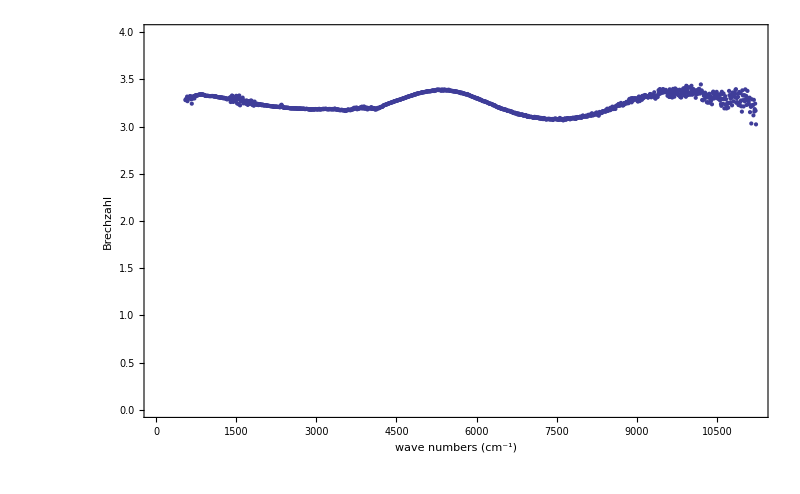

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahl=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]
```

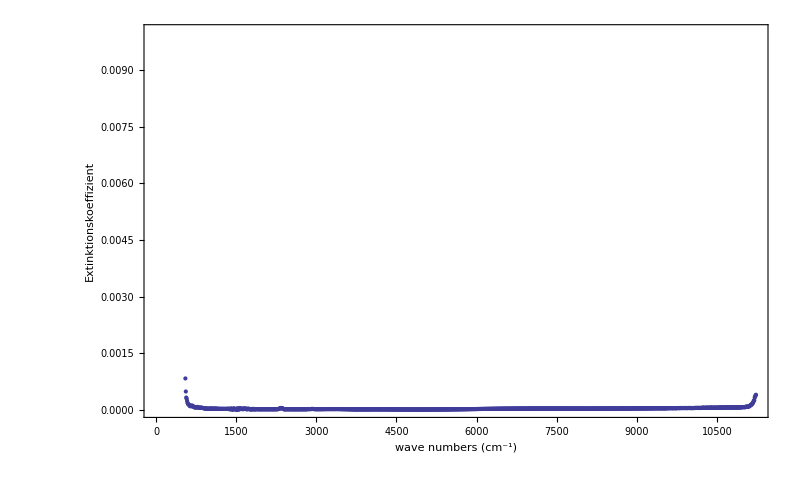

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizient=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{0,0.01}]
```

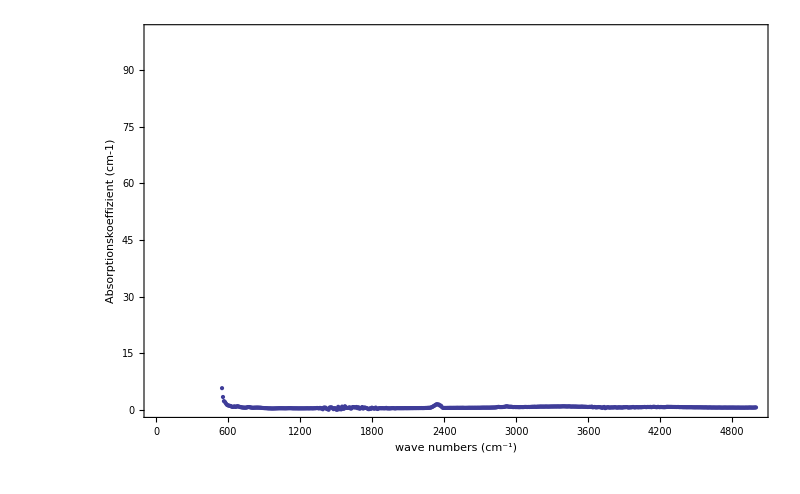

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizient=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{0,100}]
```